```mathematica
ClearAll;
d = 10;
T = 60*8;
minLocalFitValue = 1.0;
f[t_,x_,importance_] := importance/(x/d)*ⅇ^(-t/T);
```

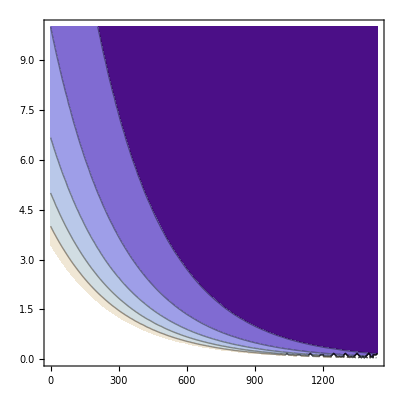

```mathematica
ContourPlot[f[t,x,1.0],{t,0,60*24},{x,0,d}]
```

```mathematica
ⅇ^(-3600*24/T)==x/d;
3600*24/T = -log(x/d);
T = 3600*24 / log(d/x);
```

```mathematica
3600*24/Log[d/0.5]
```

```mathematica
28841.028540076866/3600
```

8.0114